```mathematica
并联耦合摆的解算程序
```

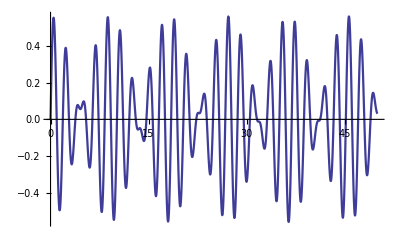

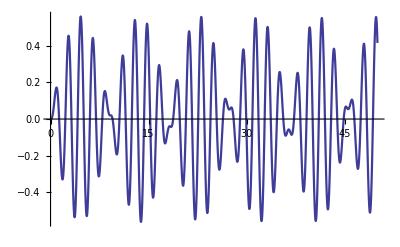

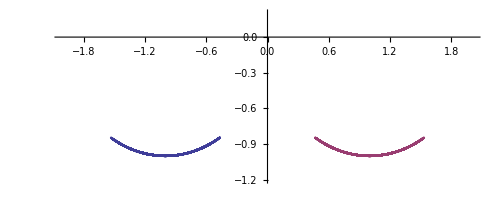

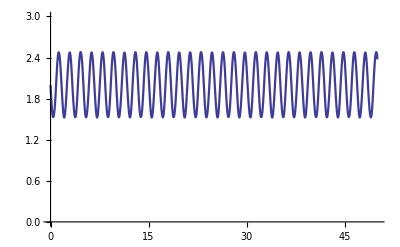

```mathematica
g=9.8;width=2;m1=0.2;m2=0.2;
L=1;k=0.5;tm=50;
initial1={0,1.9/L};initial2={0,0/L};
p1=(width-L(Sin[θ1[t]]-Sin[θ2[t]]))^2;
p2=L^2 (Cos[θ1[t]]-Cos[θ2[t]])^2;L12=√(p1+p2);
equs={θ1''[t]==
(width/L Cos[θ1[t]]+Sin[θ2[t]-θ1[t]]) k/m1 
(1-width/L12)-g/L Sin[θ1[t]],
θ2''[t]==
-(width/L Cos[θ2[t]]+Sin[θ2[t]-θ1[t]]) k/m2 
(1-width/L12)-g/L Sin[θ2[t]],
θ1[0]==initial1[[1]],θ1'[0]==initial1[[2]],
θ2[0]==initial2[[1]],θ2'[0]==initial2[[2]]};
s=NDSolve[equs,{θ1,θ2},{t,0,tm}];
{θ1,θ2}={θ1,θ2}/.s[[1]];
Plot[θ1[t],{t,0,tm},PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Plot[θ2[t],{t,0,tm},PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
ParametricPlot[
Evaluate[{{L Sin[θ1[t]]-width/2,-L Cos[θ1[t]]},
{L Sin[θ2[t]]+width/2,-L Cos[θ2[t]]}}],
{t,0,tm},PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],
PlotRange->{{-width/2-1,width/2+1},
{-L-0.2,0.2}}]
Plot[L12,{t,0,tm},PlotRange->{{0,tm},{0,3}},
AxesOrigin->{0,0},PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Clear[g,equs,s,θ1,θ2,tm,initial1,initial2]
```